# Vector Plot and Minimization/Maximization

## Fall 2016

```mathematica
Clear["Global`*"]
```

## Vector Plot

In lecture, you’ve recently learned about the gradient of a scalar function:

∇f[x,y]=⟨f_x[x,y],f_y[x,y]⟩

We can use Mathematica to calculate the gradient:

```mathematica
f[x_,y_]=Sin[x]Sin[y];
```

```mathematica
gradf1[x_,y_]={D[f[x,y],x],D[f[x,y],y]}
```

{Cos[x] Sin[y],Cos[y] Sin[x]}

```mathematica
gradf2[x_,y_]=D[f[x,y],{{x,y}}]
```

{Cos[x] Sin[y],Cos[y] Sin[x]}

This is one example of a vector function, a function which takes in multiple variables and gives back multiple components. Because the output has multiple components, we need to visualize the function in some way other than a surface like we’ve done before. The usual way to visualize these functions is a vector plot:

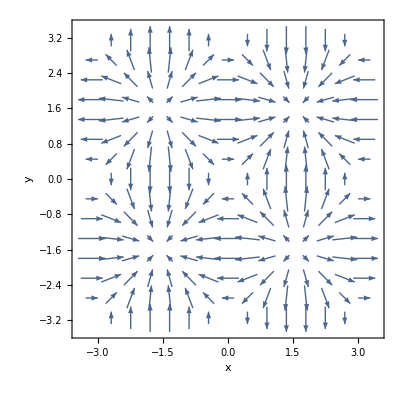

```mathematica
VectorPlot[gradf2[x,y],{x,-π,π},{y,-π,π},FrameLabel->{"x","y"}]
```

## Optimization

In Calculus 1, you learned how to use the first and second derivatves of a function of one variable to locate and classify critical points of a function. Soon, you’ll learn how to do this for functions of two variables. We can also do this easily in Mathematica with the functions FindMinimize and FindMaximize. We will need an initial guess for the location of each maxima or minima, so we should plot the function first.

```mathematica
Plot3D[f[x,y],{x,-π,π},{y,-π,π},AxesLabel->{"x","y","f[x,y]"}]
```

-Graphics3D-

So, we expect the critical points to be around (2,2), (-2,2), (2,-2), and (-2,-2):

```mathematica
cp1=FindMinimum[f[x,y],{{x,2},{y,-2}}]
```

{-1.,{x→1.5708,y→-1.5708}}

```mathematica
cp2=FindMinimum[f[x,y],{{x,-2},{y,2}}]
```

{-1.,{x→-1.5708,y→1.5708}}

```mathematica
cp3=FindMaximum[f[x,y],{{x,2},{y,2}}]
```

{1.,{x→1.5708,y→1.5708}}

```mathematica
cp4=FindMaximum[f[x,y],{{x,-2},{y,-2}}]
```

{1.,{x→-1.5708,y→-1.5708}}

Suppose that we wanted to use the location later on, say to verify that the first derivatives were zero, then we’d need to use the “slash-dot” notation:

```mathematica
D[f[x,y],x]/.cp1[[2]] (* we want to use the second element of the cp1 list, so we say [[2]] *)
D[f[x,y],y]/.cp1[[2]]
```

5.08808×10^-9

-5.08808×10^-9